# Exercise 13

As with all of the exercises you will complete in this course, you will be expected to turn your *.nb file in to the course TA before the next lecture.  Please do so by e-mailing your completed exercise file to Lan Yu (ece329.uiuc@gmail.com), make sure you name the file using the following notation: “Exn_Last_First.nb”, where n is the Exercise number (in this case, 13), and First and Last would be your first and last name.  So my submission to Lan for this exercise would be titled “Ex13_Dan_Wasserman.nb”.  You will receive full credit for your exercise if it turned in before the next lecture (Lecture n+1).  No late submissions will be accepted.

## Objective/Overview:

In today’s exercise, we are going to go deeper into Faraday’s Law, which we first discussed in our last lecture.

```mathematica
ClearAll[r, dr, f, rsurf, dsurf, fsurf, flux, b1, emf1,bwire0cyl,bwirecyl, rmoving, drmoving, emf2,vcrossBdr,bwirecylt]
```

## Faraday’s Law and Electromotive Force

In class we were introduced to Faraday’s Law, which tells us that ∇×E⃗=-(ⅆ B⃗)/ⅆt.  We used this to show that the work done on a charge moving around a circular path, enclosing a magnetic flux, depends on the time rate of change of the magnetic flux  
ℰ=∮(E⃗+v⃗×B⃗)·ⅆ ℓ⃗=-ⅆ/ⅆt∫B⃗·d S⃗=-ⅆΨ/ⅆt
There are a number of ways to change the magnetic flux through a surface:
1.  You could have a fixed loop, and vary the magnetic field in time: S constant, B⃗->B⃗(t)
2. You could have a loop that rotates in space, and a fixed magnetic field: S rotating, B⃗ constant
3. You could have a loop of fixed shape, and move that loop through a magnetic field that varies spatially: S moving, B⃗->B⃗(x,y,z)
4.  You could have a constant magnetic field, but change the shape of your surface: S changing, B⃗ constant
5.  Any combination of the above!!
In today’s lecture we are going to calculate the electromotive force generated in a wire loop from some of the above scenarios.  To simplify matters, we are going to use the same basic geometry for our loop: a circle of radius r, centered at {xo,yo,zo}.  Let’s make things easier by assuming that the loop lies in a plane parallel to the xy plane.  

To prove that Faraday’s Law works, we will look at both sides of the expression ∮(E⃗+v⃗×B⃗)·ⅆ ℓ⃗=-ⅆΨ/ⅆt, to show that they are equivalent, but then we will quickly move on to just using the right side of the expression, since it will be the easiest to calculate.

Let’s remind ourselves how to take a line integral in Mathematica.
For a vector field F⃗(x,y,z)  and a path C, the line integral is ∫_C F⃗(x,y,z)ⅆ r⃗.  We write the path C as r⃗(t)=x(t)î+y(t)ĵ+z(t)k̂, for a range of t.  Our line integral is then: ∫_C F⃗(x(t),y(t),z(t))r⃗'(t).
So let’s take the integral of a field F⃗(x,y,z) =xî+xk̂ over a circular loop of radius r=1 centered at {0,0,0} and lying in the xy plane.

```mathematica
r={Cos[2*Pi*t],Sin[2*Pi*t],0}
```

{Cos[2 π t],Sin[2 π t],0}

```mathematica
dr=D[r,t]
```

{-2 π Sin[2 π t],2 π Cos[2 π t],0}

```mathematica
f={Cos[2*Pi*t],0,Cos[2*Pi*t]}
```

{Cos[2 π t],0,Cos[2 π t]}

```mathematica
Integrate[Dot[f,dr],{t,0,1}]
```

0

What about a surface integral?  We should be able to do that too!  For the disk bounded by the path we used in the above example, we can find the surface integral of F⃗ through S.  This is kind of tricky, so bear with me...
Our surface is a disk, which we can define by

```mathematica
rsurf={rd*Cos[theta],rd*Sin[theta],0}
```

{rd Cos[theta],rd Sin[theta],0}

For a surface parameterized by two parameters (rd and theta, in this case), ⅆ S⃗=(ⅆrsurf/ⅆrd×ⅆrsurf/ⅆtheta)

```mathematica
dsurf=Cross[D[rsurf,rd],D[rsurf,theta]]
```

{0,0,rd Cos[theta]^2+rd Sin[theta]^2}

```mathematica
fsurf={rd*Cos[theta],0,rd*Cos[theta]}
```

{rd Cos[theta],0,rd Cos[theta]}

```mathematica
flux=Integrate[Dot[fsurf,dsurf],{rd,0,1},{theta,0,2*Pi}]
```

0

Let’s make sure we are not crazy, and calculate the flux through our disk for a constant field  F⃗(x,y,z) =k̂, which we know should give us πr^2

```mathematica
Integrate[Dot[{0,0,1},dsurf],{theta,0,2*Pi},{rd,0,1}]
```

π

Cool!  Let’s get to work!

### Electromotive Force from a Time-Varying Magnetic Field

Let’s assume we have a magnetic field B⃗(t)=10Cos[10πt]k̂[T].  Calculate the electromotive force, as a function of time, generated around our loop.
We know we can use the same ⅆ S⃗=dsurf as we did above.

```mathematica
b1={0,0,10*Cos[10*Pi*t]}
```

{0,0,10 Cos[10 π t]}

```mathematica
emf1=-D[Integrate[Dot[b1,dsurf],{theta,0,2*Pi},{rd,0,1}],t]
```

100 π^2 Sin[10 π t]

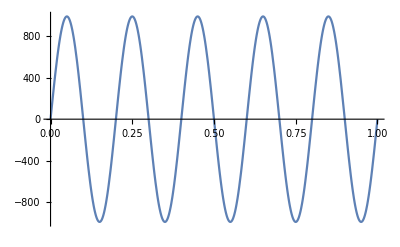

```mathematica
Plot[emf1,{t,0,1}]
```

We see that a time varying magnetic field leads to a time varying electromotive force around our loop!!  Since ℰ=∮(E⃗+v⃗×B⃗)·ⅆ ℓ⃗, and v=0 in this situation, this means that an electric field exists along our wire, which will drive a current around the wire loop (we’ll get to this current, eventually!).

### Electromotive Force from Motion through a spatially-varying Magnetic Field

Let’s now consider a magnetic field generated from an infinite wire carrying a current of I=1A.  We will place the wire pointing in the +ŷ direction, at x=-2, z=0.  If we drag our loop at a constant velocity v⃗=2x̂ [m/s], starting at {0,0,0} at t=0.

```mathematica
muo=1.257*10^-6
```

1.257×10^-6

The expression for the magnetic field of a 1A wire in the ŷ direction going through the origin is:

```mathematica
bwire0cyl={0,muo/(2*Pi*r1)}
```

{0,(2.00058×10^-7)/r1}

```mathematica
TransformedField["Polar"->"Cartesian",bwire0cyl,{r1,θ}->{x,z}]
```

Making sure we follow the right hand rule, and shifting the wire to x=-2, we get the B field of this system to be:

```mathematica
bwirecyl={(2.000577634665124*^-7 z)/((x+2)^2+z^2),0,(-2.000577634665124*^-7 (x+2))/((x+2)^2+z^2)}
```

{(2.00058×10^-7 z)/((2+x)^2+z^2),0,-(2.00058×10^-7 (2+x))/((2+x)^2+z^2)}

Let’s plot this for a sanity check:

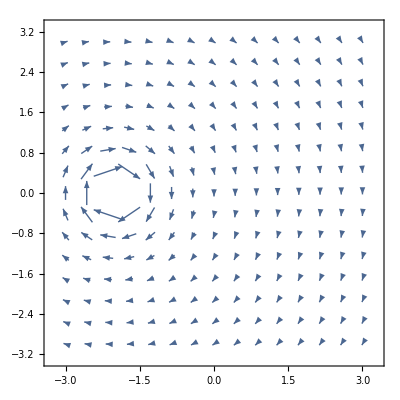

```mathematica
VectorPlot[Boole[(x+2)^2+z^2≥0.1]{bwirecyl[[1]],bwirecyl[[3]]},{x,-3,3},{z,-3,3}]
```

Looks Good!
There are two ways to find the emf.  We can take the surface integral of BdS as a function of time, or we can calculate the line integral around the loop.  Let’s try the latter here:

```mathematica
rmoving={2*t+Cos[2*Pi*theta],Sin[2*Pi*theta],0}
```

{2 t+Cos[2 π theta],Sin[2 π theta],0}

```mathematica
drmoving=D[rmoving,theta]
```

{-2 π Sin[2 π theta],2 π Cos[2 π theta],0}

Our B, in parametric terms, along the path of the circle, is:

```mathematica
bwirecylt={0,0,(-2.000577634665124*^-7 (2*t+Cos[2*Pi*theta]+2))/(2*t+Cos[2*Pi*theta]+2)^2}
```

{0,0,-(2.00058×10^-7)/(2+2 t+Cos[2 π theta])}

The cross product of of v and B :

```mathematica
vcrossB=Simplify[Cross[{2,0,0},bwirecylt]]
```

{0.,(4.00116×10^-7)/(2+2 t+Cos[2 π theta]),0}

We take the dot product of v x B with dr:

```mathematica
vcrossBdr=Dot[vcrossB,drmoving]
```

0.+(2.514×10^-6 Cos[2 π theta])/(2+2 t+Cos[2 π theta])

And then the line integral...basically integrate over theta from 0 to 1

```mathematica
emf2=Integrate[(2.514*10^-6 Cos[2 π theta])/(2+2 t+Cos[2 π theta]),{theta,0,1}]
```

2.514×10^-6 (1-(2 (1+t) √((1+2 t)/(3+2 t)))/(1+2 t))

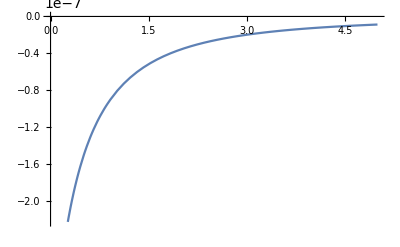

```mathematica
Plot[emf2,{t,0,5}]
```

Now calculate the emf generated around the loop assuming the loop is moving in the +z direction with a velocity v⃗=2 k̂[m/s], starting at {0,0,0} at t=0.

{Cos[2 π theta],Sin[2 π theta],2 t}

{-2 π Sin[2 π theta],2 π Cos[2 π theta],0}

{(4.00116×10^-7 t)/(4 t^2+(2+Cos[2 π theta])^2),0,-(2.00058×10^-7 (2+Cos[2 π theta]))/(4 t^2+(2+Cos[2 π theta])^2)}

{0.,(8.00231×10^-7 t)/(4 t^2+(2+Cos[2 π theta])^2),0.}

0.+(5.028×10^-6 t Cos[2 π theta])/(4 t^2+(2+Cos[2 π theta])^2)

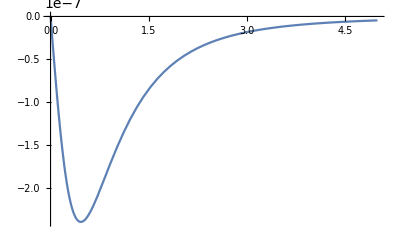

```mathematica
rmoving2={Cos[2*Pi*theta],Sin[2*Pi*theta],2*t}
drmovingz=D[rmoving2,theta]
bwirecylt2={(2.000577634665124*^-7 (2*t))/((Cos[2*Pi*theta]+2)^2+(2*t)^2),0,(-2.000577634665124*^-7 (Cos[2*Pi*theta]+2))/((Cos[2*Pi*theta]+2)^2+(2*t)^2)}
vcrossB2=Simplify[Cross[{0,0,2},bwirecylt2]]
vcrossBdr2=Dot[vcrossB2,drmovingz]
emf3=Integrate[(5.027999999999999*^-6 t Cos[2 π theta])/(4 t^2+(2+Cos[2 π theta])^2),{theta,0,1}]
Plot[emf3,{t,0,5}]
```